# Implementing a Visualizer for DNA Sequence Alignments

Jessica Shi

Mentor: Lauren Cooper

## By: Jessica Shi

## Overview

This project creates a visualization function that takes an input of a reference DNA sequence and multiple comparison sequences and outputs several different visual models that show the similarities and differences between them. It utilizes the functions, SequenceAlignment, LongestCommonSubsequence, NeedlemanWunschSimilarity, and SmithWatermanSimilarity, which are built-in functions of the WolframLanguage that use the classic algorithms for sequence alignment as created by the researchers Needleman, Wunsch , Smith, and Waterman. The result will yield figures and graphs to show the alignment . This tool can be used to study evolutionary origins of species, detect mutations, and analyze other biological relationships.

## Introduction

In the field of bioinformatics, DNA sequence alignment is a method of arranging sequences to find similarities between them. These similarities may be caused by similar function, structure, or evolutionary origin. More than 25% implies potential for similar function, and 18-25% implies similar structure or function. Keep in mind that close identity between sequence does not imply any correlation, they can be completely unrelated. These alignments are generated by computer algorithms. There are two types, pairwise alignment and multi - sequence alignment. For this project, I only used pairwise alignment. The two types of pairwise alignment are global alignment and local alignment developed by Needleman/Wunsch and Smith/Waterman respectively. Global alignment attempts to align the sequences along the entire input, while local alignment aligns within a fixed distance from the current character. My goal was to create a visual output that represents sequence alignment.

## Randomly Generate Test DNA Sequences

The following functions create random data that can be used to test the functionality of other functions.

```mathematica
random[n_]:=StringJoin@RandomChoice[{"A","T","G","C"},n]
```

```mathematica
randomdata1[n_]:={random[n],random[n]}
```

```mathematica
randomdata2[a_,b_]:={random[a],Table[random[a],b]}
```

```mathematica
randomdata3[a_,b_]:={random[a],random[b]}
```

```mathematica
randomdata4[a_,b_]:={random[a],Table[random[RandomInteger[{7000,12000}]],b]}
```

I generated several test sequences using the above functions that will be used as examples later in the notebook:

```mathematica
test=randomdata1[1000];
Short@test
```

{CTAGCAACAGATTAGCGAAGCTCTAGTAACGC…CTGCGCTAGCCCGCCGTAGAGCGCGAGACTATC,…}

```mathematica
test2=randomdata1[5000];
Short@test2
```

{GTGAAATCATCGCCGGCTTGGTCTGCTTCGAT…AATCGTATGCGGACGGAAGCGGGACGACGTCTT,…}

```mathematica
test3=randomdata2[3000,5];
Short@test3
```

{GGTCAACATGAGACCTACGAACGAATTTCAGC…AAGAGTTTCCCTCCGCGGTGTCTCTTTCAGGAT,{«1»}}

## Alignment Visualizer

First, a colored image representing sequence alignment between two sequences is created through the picture function.  My initial goal was to create an alignment visualizer similar to the commercial sequence alignment visualizations. This entailed lining up the similar bases in columns that are easily differentiated, and showing the bases that differ as well. This meant it would be necessary to insert spaces when bases were present in one strand and absent in the other. I researched the different types of alignment, and I decided to start with pairwise alignment and possibly expand towards multi-sequence alignment.

	My first thought was to begin developing an algorithm to align the sequences, but I realized, to my delight, that there were various built-in tools that help with biological computation including the functions SequenceAlignment, LongestCommonSubsequence, NeedlemanWunschSimilarity, and SmithWatermanSimilarity.

	I started playing around with the SequenceAlignment results, and tried to make the visualizer with the lined-up columns. This proved to be difficult task. After some research, I discovered a Wolfram Demonstration that used the alignment function to align English dictionary words. Its formatting structure proved to be helpful, and I was able to format the SequenceAlignment results as desired. I also added a color association to color the letters A,T,G,C in different colors. This is how it works:

Removes spaces and line breaks and format into a framed row

```mathematica
picture[d_String,e_String]:=Text@Row[Flatten@(Map[format,SequenceAlignment[StringDelete[ToUpperCase[d]," "|"\n"|"\t"],StringDelete[ToUpperCase[e]," "|"\n"|"\t"],MergeDifferences->False]]),Frame->True]
```

Formats each term of the output of Sequence Alignment and assign coloring for matches/substitutions/insertions/deletions

```mathematica
format[{a_String,b_String}]:=Column[{colored[a],colored[b]},Spacings->1,Background->Blend[{LightRed,White},.17]];
format[{a_String,""}]:=Column[{colored[a],StringJoin@Table["-",{StringLength[a]}]},Spacings->1,Background->Blend[{LightRed,Red},.12]];
format[{"",b_String}]:=Column[{StringJoin@Table["-",{StringLength[b]}],colored[b]},Spacings->1,Background->Blend[{LightRed,Red},.12]];
format[c_String]:=If[StringLength[c]>20,format2/@StringPartition[c,10],format2[c]];
```

```mathematica
format2[c_String]:=Column[{colored[c],colored[c]},Spacings->1,Background->LightGreen];
```

Colors and emboldens the sequence code

```mathematica
colored[h_String]:=Row@(colorassoc/@Characters[h])
```

```mathematica
colorassoc=<|"A"->Style["A",RGBColor[1.,0.02,0.87],Bold],"T"->Style["T",Blue,Bold],"G"->Style["G",RGBColor[0.15,0.67,1.],Bold],"C"->Style["C",RGBColor[0.34,0.34,0.34],Bold]|>
```

<|A→A,T→T,G→G,C→C|>

Only displays alignment for first 1000

```mathematica
picturelong[a_,b_]:=picture[StringTake[a,1000],StringTake[b,1000]]
```

This is an example output for two random sequences of 1000:

```mathematica
picture[First@test,test[[2]]]
```

-Graphics-

## Color Chain

The next step was to create a visual for very long sequences- something that would be easier to look at rather than the detailed alignment visual.Some genes are only a couple hundred bases long, but most genes are thousands and thousands of bases long. I found an interesting example of alignment visualization for the human genotype compared to other primates. They used chains of colors with different percentage values to measure the percentage of difference in each 500,000 bases of the genomes. I decided to create a similar visual at a smaller scale.

	For shorter sequences that are less than 10,000 bases, the sequences are analyzed in groupings of 100. For longer sequences that are more than 10,000 bases, the sequences are analyzed in groupings of 1000. One disk is generated for each chunk and is colored according to the percent similar bases it has with the reference sequence.

Makes the longer string the same length as the shorter string

```mathematica
samelength[{a_,b_}]:=If[StringLength[a]>StringLength[b],{StringTake[a,StringLength[b]],b},{a,StringTake[b,StringLength[a]]}]
```

Transposes the partition of each string into 100 or 1000 based on the length.

```mathematica
split[{a_,b_}]:=If[StringLength[b]<10000,Transpose[{StringPartition[a,100],StringPartition[b,100]}],Transpose[{StringPartition[a,1000],StringPartition[b,1000]}]]
```

Calculates the number of similar bases

```mathematica
basecount[{a_,b_}]:=If[StringLength[b]<10000,samebase[First@#,#[[2]]]&/@split[samelength[{a,b}]],Round/@(Divide[#,10]&/@(samebase[First@#,#[[2]]]&/@split[samelength[{a,b}]]))]
```

Creates the color chain as a table of colored disks from the redgreen association

```mathematica
colormap[{a_,b_}]:=Graphics@Table[Style[Disk[{n,0},StringLength[a]/5000],(redgreen/@basecount[{a,b}])[[n]]],{n,1,Length@(redgreen/@basecount[{a,b}]),1}]
```

Generates an association that assigns each numerical value 1-100 to a color from red to green

```mathematica
redgreen=Join[AssociationThread[Range[0,49]->Reverse@Table[Darker[Red,n],{n,0,.49,0.01}]],AssociationThread[Range[50,74]->Table[Hue[n],{n,0,.36,0.015}]],AssociationThread[Range[75,100]->Table[Darker[Green,n],{n,0,.75,.03}]]]
```

<|0→RGBColor[0.51, 0., 0.],1→RGBColor[0.52, 0., 0.],2→RGBColor[0.53, 0., 0.],3→RGBColor[0.54, 0., 0.],4→RGBColor[0.55, 0., 0.],5→RGBColor[0.56, 0., 0.],6→RGBColor[0.5700000000000001, 0., 0.],7→RGBColor[0.5800000000000001, 0., 0.],8→RGBColor[0.59, 0., 0.],9→RGBColor[0.6, 0., 0.],10→RGBColor[0.61, 0., 0.],11→RGBColor[0.62, 0., 0.],12→RGBColor[0.63, 0., 0.],13→RGBColor[0.64, 0., 0.],14→RGBColor[0.6499999999999999, 0., 0.],15→RGBColor[0.6599999999999999, 0., 0.],16→RGBColor[0.6699999999999999, 0., 0.],17→RGBColor[0.6799999999999999, 0., 0.],18→RGBColor[0.69, 0., 0.],19→RGBColor[0.7, 0., 0.],20→RGBColor[0.71, 0., 0.],21→RGBColor[0.72, 0., 0.],22→RGBColor[0.73, 0., 0.],23→RGBColor[0.74, 0., 0.],24→RGBColor[0.75, 0., 0.],25→RGBColor[0.76, 0., 0.],26→RGBColor[0.77, 0., 0.],27→RGBColor[0.78, 0., 0.],28→RGBColor[0.79, 0., 0.],29→RGBColor[0.8, 0., 0.],30→RGBColor[0.81, 0., 0.],31→RGBColor[0.8200000000000001, 0., 0.],32→RGBColor[0.83, 0., 0.],33→RGBColor[0.84, 0., 0.],34→RGBColor[0.85, 0., 0.],35→RGBColor[0.86, 0., 0.],36→RGBColor[0.87, 0., 0.],37→RGBColor[0.88, 0., 0.],38→RGBColor[0.89, 0., 0.],39→RGBColor[0.9, 0., 0.],40→RGBColor[0.91, 0., 0.],41→RGBColor[0.92, 0., 0.],42→RGBColor[0.9299999999999999, 0., 0.],43→RGBColor[0.94, 0., 0.],44→RGBColor[0.95, 0., 0.],45→RGBColor[0.96, 0., 0.],46→RGBColor[0.97, 0., 0.],47→RGBColor[0.98, 0., 0.],48→RGBColor[0.99, 0., 0.],49→RGBColor[1., 0., 0.],50→Hue[0.],51→Hue[0.015],52→Hue[0.03],53→Hue[0.045],54→Hue[0.06],55→Hue[0.075],56→Hue[0.09],57→Hue[0.105],58→Hue[0.12],59→Hue[0.135],60→Hue[0.15],61→Hue[0.16499999999999998],62→Hue[0.18],63→Hue[0.195],64→Hue[0.21],65→Hue[0.22499999999999998],66→Hue[0.24],67→Hue[0.255],68→Hue[0.27],69→Hue[0.285],70→Hue[0.3],71→Hue[0.315],72→Hue[0.32999999999999996],73→Hue[0.345],74→Hue[0.36],75→RGBColor[0., 1., 0.],76→RGBColor[0., 0.97, 0.],77→RGBColor[0., 0.94, 0.],78→RGBColor[0., 0.91, 0.],79→RGBColor[0., 0.88, 0.],80→RGBColor[0., 0.85, 0.],81→RGBColor[0., 0.8200000000000001, 0.],82→RGBColor[0., 0.79, 0.],83→RGBColor[0., 0.76, 0.],84→RGBColor[0., 0.73, 0.],85→RGBColor[0., 0.7, 0.],86→RGBColor[0., 0.67, 0.],87→RGBColor[0., 0.64, 0.],88→RGBColor[0., 0.61, 0.],89→RGBColor[0., 0.5800000000000001, 0.],90→RGBColor[0., 0.55, 0.],91→RGBColor[0., 0.52, 0.],92→RGBColor[0., 0.49, 0.],93→RGBColor[0., 0.45999999999999996, 0.],94→RGBColor[0., 0.43000000000000005, 0.],95→RGBColor[0., 0.4, 0.],96→RGBColor[0., 0.37, 0.],97→RGBColor[0., 0.3400000000000001, 0.],98→RGBColor[0., 0.31000000000000005, 0.],99→RGBColor[0., 0.28, 0.],100→RGBColor[0., 0.25, 0.]|>

Creates a scale for user reference for the redgreen association

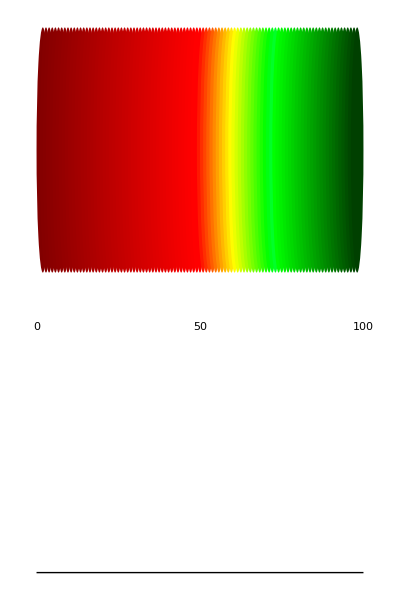

```mathematica
redgreenscale=Column[{Graphics@Table[Style[Disk[{n,0},2],Values[redgreen][[n]]],{n,1,Length[redgreen],1}],Graphics[{Line[{{0,0},{20,0}}],Text[0,{0,1}],Text[50,{10,1}],Text[100,{20,1}]}]}]
```

Here is an example output for two random sequences of 5000:

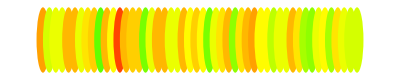

```mathematica
colormap[test2]
```

## Chart and Value functions

These following functions are various other calculated numerical values for the overall analysis table, which can provide valuable information when analyzing sequence alignment.

Returns the number of similar bases from the SequenceAlignment

```mathematica
samebase[f_String,g_String]:=StringLength@StringJoin@Cases[SequenceAlignment[StringDelete[ToUpperCase[f]," "|"\n"|"\t"],StringDelete[ToUpperCase[g]," "|"\n"|"\t"]],_String,1]
```

```mathematica
samebase[First@test,test[[2]]]
```

634

Represents the amount of similar bases using a percentage

```mathematica
percent[{a_,b_}]:=PercentForm[(samebase[a,b]/(StringLength[b])//N)]
```

```mathematica
percent[test]
```

63.4%

Generates a pie chart for similarities and differences between two sequences

```mathematica
pie[d_String,e_String]:=PieChart[{samebase[d,e],StringLength[d]-samebase[d,e]},ChartLabels->{"similarities","differences"},PlotLabel->"Comparison Pie Chart",
ChartStyle->{LightGreen,LightRed}]
```

```mathematica
pie[First@test,test[[2]]]
```

-Graphics-

Generates a more efficient pie chart for only the first 1000 bases for 2 long sequences

```mathematica
pielong[d_,e_]:=PieChart[{samebase[StringTake[d,1000],StringTake[e,1000]],1000-samebase[StringTake[d,1000],StringTake[e,1000]]},ChartLabels->{"similarities","differences"},PlotLabel->"Comparison Pie Chart",
ChartStyle->{LightGreen,LightRed}]
```

Creates a BarChart that shows the count of ATGC bases in each sequence

```mathematica
bar[a_String,b_String]:=BarChart[{{Count[Characters[a],"A"|"a"],Count[Characters[a],"T"|"t"],Count[Characters[a],"G"|"g"],Count[Characters[a],"C"|"c"]},{Count[Characters[b],"A"|"a"],Count[Characters[b],"T"|"t"],Count[Characters[b],"G"|"g"],Count[Characters[b],"C"|"c"]}},]
```

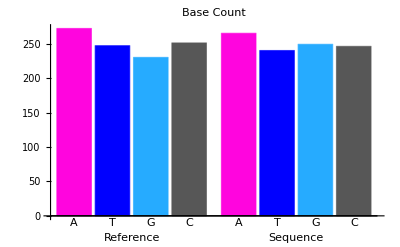

```mathematica
bar[First@test,test[[2]]]
```

Maps the S-W Similarity and N-W Similarity functions to the reference and list of sequences

```mathematica
comparisonSW[reference_String,compare_List]:=Map[SmithWatermanSimilarity[reference,#]&,compare]
```

```mathematica
comparisonNW[reference_String,compare_List]:=Map[NeedlemanWunschSimilarity[reference,#]&,compare]
```

Uses the results of the above results to generate a comparison BarChart

```mathematica
nwbar[a_String,b_List]:=BarChart[comparisonNW[a,b],]
```

```mathematica
swbar[a_String,b_List]:=BarChart[comparisonSW[a,b],]
```

TabView for global/local alignment BarCharts

```mathematica
gltab[{a_,b_}]:=TabView[{"Global Alignment"->nwbar[a,b],"Local Alignment"->swbar[a,b]}]
```

```mathematica
gltab[test3]
```

12

Creates a BarChart that incorporates the samebase and sequence length for all of the sequences

```mathematica
barall[{a_String, b_List}]:=Column[{barallopen,BarChart[Prepend[({samebase[a,#],(StringLength[#]-samebase[a,#])}&/@b),{StringLength[a],0}],ChartLayout->"Stacked",ChartLabels->{Prepend[StringJoin[{"Seq ",ToString@#}]&/@Range[1,Length[b]],"Ref"],{"",""}},ChartLegends->{"Similar","Different"},AxesLabel->"Number of Bases",ChartStyle->{Green,Red},ImageSize->"Medium"]},Center]
```

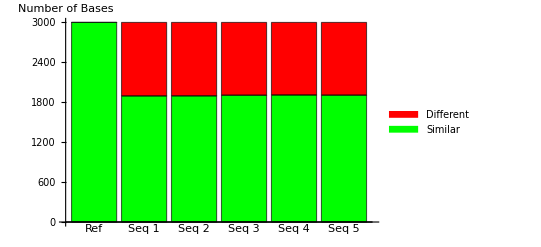

```mathematica
barall[test3]
```

## Checkboxes

I created checkboxes to allow the user to open and minimize the visuals in the table to allow for easier viewing. When the checkbox is True it displays the visual, and when it is False it displays a blank string. The checkbox differs for short and long sequences for the alignment visual and the PieChart so the program can run more quickly.

Checkboxes for the alignment visual

```mathematica
check[a_,b_]:=DynamicModule[{x},Grid[{{Checkbox[Dynamic[x]],Dynamic[If[x,picture[a,b],""]]}}]]
```

```mathematica
checklong[a_,b_]:=DynamicModule[{x},Grid[{{Checkbox[Dynamic[x]],Dynamic[If[x,picturelong[a,b],""]]}}]]
```

Checkboxes for the PieChart

```mathematica
piecheck[a_,b_]:=DynamicModule[{x},Grid[{{Checkbox[Dynamic[x]],Dynamic[If[x,pie[a,b],""]]}}]]
```

```mathematica
piechecklong[a_,b_]:=DynamicModule[{x},Grid[{{Checkbox[Dynamic[x]],Dynamic[If[x,pielong[a,b],""]]}}]]
```

Checkbox for the BarChart

```mathematica
barcheck[a_,b_]:=DynamicModule[{x},Grid[{{Checkbox[Dynamic[x]],Dynamic[If[x,bar[a,b],""]]}}]]
```

This is an example checkbox for a alignment visual:

```mathematica
check[First@test,test[[2]]]
```

## Openers and Explanations

I created explanations that are accessed by OpenerView for each one of the visuals or values that may be confusing for the user to understand.

ATGC base count bar chart explanation

```mathematica
baropen=OpenerView[{"display bar chart", }];
```

Color chain explanation

```mathematica
colorchainopen=OpenerView[{"colorchain", redgreenscale}];
```

Local alignment score explanation

```mathematica
laopen=OpenerView[{"local alignment score",}];
```

Global alignment score explanation

```mathematica
gaopen=OpenerView[{"global alignment score",}];
```

Longest common subsequence explanation

```mathematica
lcsopen=OpenerView[{"longest common subsequence",}];
```

Percent similarity explanation

```mathematica
peropen=OpenerView[{"% similar",}];
```

Alignment visual explanation

```mathematica
alignopen=OpenerView[{"show alignment (first 1000)",}];
```

PieChart explantion

```mathematica
pieopen=OpenerView[{"show pie chart",}];
```

Number of common bases explanation

```mathematica
cbopen=OpenerView[{"# of common bases",}];
```

Base count comparison BarChart explanation

```mathematica
barallopen=OpenerView[{"Base Count Comparison",}];
```

This is the one example of the OpenerView with the explanation:

```mathematica
barallopen
```

## Generate Table for Multiple Sequence Comparison

I created a functions to generate the data necessary for the two tables, and then I created and formatted the tables. Lastly, they were combined with the comparison bar graphs to generate the final tables function. That takes in an input of one reference sequence and multiple comparison sequences, and returns the numerical value table, a visual table, and the comparative BarCharts.

Generates the data for the first table with numerical values

```mathematica
gendata[a_String,b_String,c_List]:={StringJoin[{"Sequence ",ToString@First@Flatten@Position[c,b]}],If[StringLength[b]>30,StringTake[b,30],b],StringLength[b],LongestCommonSubsequence[a,b],SmithWatermanSimilarity[a,b],NeedlemanWunschSimilarity[a,b],samebase[a,b],percent[{a,b}]}
```

Creates a table with checkboxes that access the visuals and charts

```mathematica
gendata2[a_String,b_String,c_List]:={StringJoin[{"Sequence ",ToString@First@Flatten@Position[c,b]}],colormap[{a,b}],If[(StringLength@b>1000),checklong[a,b],check[a,b]],barcheck[a,b],If[(StringLength@b)>1000,piechecklong[a,b],piecheck[a,b]]}
```

Formats the data from gendata into a grid

```mathematica
table[{a_String,b_List}]:=Text@Grid[Prepend[Prepend[Map[gendata[a,#,b]&,b],{"Reference",If[StringLength[a]>30,StringTake[a,30],a],StringLength[a]}],{"name","first 30 bases","length of sequence",lcsopen,laopen,gaopen,cbopen,peropen}],]
```

Formats the data from gendata2 into a grid

```mathematica
table2[{a_String,b_List}]:=Text@Grid[Prepend[Map[gendata2[a,#,b]&,b],{"name",colorchainopen,alignopen, baropen,pieopen}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},
Frame->All]
```

Combines table, table 2, barall and gltab into one function

```mathematica
tables[{a_String,b_List}]:=Column[{table[{a,b}],table2[{a,b}],Row[{barall[{a,b}],gltab[{a,b}]}]}]
```

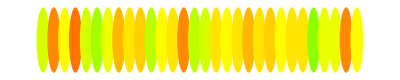
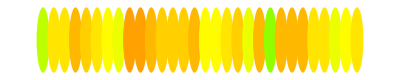
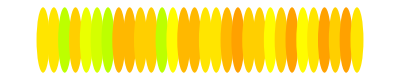
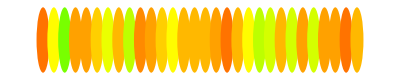
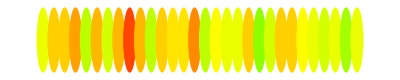
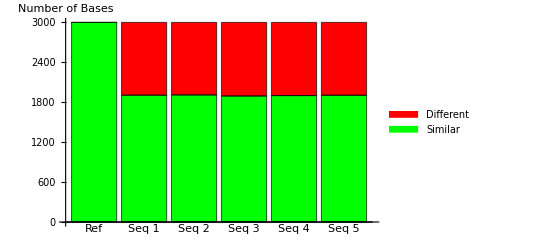
name | first 30 bases | length of sequence |  |  |  |  | 
Reference | GTGCTATCTATCGTCGCGTTGGGTACACCC | 3000 |  |  |  |  | 
Sequence 1 | AATTTCCCGGAGGTAACGGCTATCTCGGAT | 3000 | ATATTCATTAA | 353. | 304. | 1906 | 63.53%
Sequence 2 | CATTTCACGCTCTCCCGGTCACATTAGACA | 3000 | GGGTGGATACAG | 345. | 323. | 1910 | 63.67%
Sequence 3 | CGGACAAATCAATAGGCAGCACTCACATAC | 3000 | TAAGCTTCCAGCC | 321. | 300. | 1894 | 63.13%
Sequence 4 | CATACCCCCGCAAAACGCCTCTGAGCGACT | 3000 | CGGAACCTGA | 346. | 322. | 1901 | 63.37%
Sequence 5 | TATCAGTCTACGAGGGGACCCAATGATGAA | 3000 | TTTCGAAATGG | 331. | 320. | 1905 | 63.5%
name |  |  |  | 
Sequence 1 | -Graphics- |  |  | 
Sequence 2 | -Graphics- |  |  | 
Sequence 3 | -Graphics- |  |  | 
Sequence 4 | -Graphics- |  |  | 
Sequence 5 | -Graphics- |  |  | 

-Graphics-12

```mathematica
tables[test3]
```

## Creating an User-Based Interface

My last task was to create an interface implementing my function to allow a user to easily access the tool. The user can choose what they want to be analyzed, and the tables function will be applied to their input. The first one I made allows the user to input their own DNA sequences for analysis.

```mathematica
freeforminput=Column[{Style["DNA Sequence Alignment Calculator and Visualizer",FontSize->30],Style["DNA Sequence Alignment Calculator and Visualizer: Copy and paste similar length DNA sequences for analysis. Spaces/uppercase/lowercase/linebreaks are accepted. Longer sequences will require more processing time. Click on the arrows in the table headings to learn more. The color chain will only be generated for sequences longer than 100 bases ",FontSize->15],Panel[DynamicModule[{a="reference",b="comparison sequences"},Column[{Row[{"1 text input: ",InputField[Dynamic[a],String]}], Row[{"1 or more text inputs separated by commas: ",InputField[Dynamic[b],String]}],Dynamic[tables[{a,StringSplit[b,","]}]]}]]]}]
```

DNA Sequence Alignment Calculator and Visualizer
DNA Sequence Alignment Calculator and Visualizer: Copy and paste similar length DNA sequences for analysis. Spaces/uppercase/lowercase/linebreaks are accepted. Longer sequences will require more processing time. Click on the arrows in the table headings to learn more. The color chain will only be generated for sequences longer than 100 bases

Next, I created an interface that uses imported Wolfram Data that can be accessed through a button pane.

Insulin gene data

```mathematica
insulin={Entity["Gene",{"INS",{"Species"->"HomoSapiens"}}](*human*)["ReferenceSequence"],{Entity["Gene",{"Ins",{"Species"->"DanioRerio"}}] ["ReferenceSequence"](*zebrafish*),Entity["Gene",{"INS",{"Species"->"CanisLupusFamiliaris"}}]["ReferenceSequence"](*dog*),Entity["Gene",{"INS",{"Species"->"PanTroglodytes"}}]["ReferenceSequence"](*chimp*),Entity["Gene",{"INS",{"Species"->"BosTaurus"}}]["ReferenceSequence"](*cow*),Entity["Gene",{"INS",{"Species"->"GallusGallus"}}]["ReferenceSequence"](*chicken*),Entity["Gene",{"Ins1",{"Species"->"MusMusculus"}}]["ReferenceSequence"](*mouse*)}};
```

```mathematica
grid=Grid[{{"Ref","Human"},{"Seq 1", "Zebrafish"},{"Seq 2","Dog"},{"Seq 3", "Chimp"},{"Seq 4","Cow"},{"Seq 5", "Chicken"},{"Seq 6","Mouse"}},Frame->All];
```

Lalba gene data

```mathematica
lalba={Entity["Gene",{"LALBA",{"Species"->"HomoSapiens"}}]["ReferenceSequence"](*human*),{Entity["Gene",{"LALBA",{"Species"->"CanisLupusFamiliaris"}}]["ReferenceSequence"](*dog*),Entity["Gene",{"LALBA",{"Species"->"PanTroglodytes"}}]["ReferenceSequence"](*chimp*),Entity["Gene",{"LALBA",{"Species"->"BosTaurus"}}]["ReferenceSequence"](*cow*),Entity["Gene",{"Lalba",{"Species"->"MusMusculus"}}]["ReferenceSequence"](*mouse*)}};
```

```mathematica
grid2=Grid[{{"Ref","Human"},{"Seq 1","Dog"},{"Seq 2", "Chimp"},{"Seq 3","Cow"},{"Seq 4","Mouse"}},Frame->All];
```

Cytochrome C gene data

```mathematica
cycs={Entity["Gene",{"CYCS",{"Species"->"HomoSapiens"}}]["ReferenceSequence"](*human*),{Entity["Gene",{"Cycs",{"Species"->"MusMusculus"}}]["ReferenceSequence"](*mouse*),Entity["Gene",{"Cycs",{"Species"->"RattusNorvegicus"}}]["ReferenceSequence"](*rat*),Entity["Gene",{"CYCS",{"Species"->"BosTaurus"}}]["ReferenceSequence"](*cow*),Entity["Gene",{"CYCS",{"Species"->"PanTroglodytes"}}]["ReferenceSequence"](*chimp*),Entity["Gene",{"CYCS",{"Species"->"GallusGallus"}}]["ReferenceSequence"](*chicken*),LinguisticAssistant["ReferenceSequence"](*fruitfly*)}};
```

```mathematica
grid3=Grid[{{"Ref","Human"},{"Seq 1","Mouse"},{"Seq 2", "Rat"},{"Seq 3","Cow"},{"Seq 4","Chimp"},{"Seq 5","Chicken"},{"Seq 6","Fruit Fly"}},Frame->All];
```

Histone gene data

```mathematica
histone={LinguisticAssistant["ReferenceSequence"](*human*),{LinguisticAssistant["ReferenceSequence"](*rat*),LinguisticAssistant["ReferenceSequence"](*mouse*)}};
```

```mathematica
grid4=Grid[{{"Ref","Human"},{"Seq 1","Rat"},{"Seq 2", "Mouse"}},Frame->All];
```

Create the interface with example data

```mathematica
Column[{Style["DNA Sequence Alignment Calculator and Visualizer",FontSize->30], Style["Select a gene in the button pane to view the analysis. Results may take a few seconds to appear.",FontSize->15],Manipulate[tables[gene],{gene,{insulin->"insulin"grid,lalba->"lalba"grid2,cycs->"cycs"grid3,histone->"histone"grid4}},SaveDefinitions->True]}]
```

DNA Sequence Alignment Calculator and Visualizer
Select a gene in the button pane to view the analysis. Results may take a few seconds to appear.

From analyzing some of the example data, one can infer that chimpanzees and humans are related in function and/or structure, especially in the LALBA and insulin genes. Other similar inferences can be made using the collected data.

## Conclusion

### Summary

These tools can be used to quickly analyze many sequences in reference to one sequence. Organisms that share similar bases and have similar sequence lengths and high alignment scores are more likely to have similar structure and function for that particular gene. It provides a large variety of visuals including charts and figures to compare the sequences for different purposes. It takes into account short sequence/long sequence differentiation and other syntactical differences. Possible applications include education or biological analysis.

### Future Work

In the future, I hope to implement a DNA to mRNA codon to protein translator.This could be useful for learning about DNA transcription and translation.I could also modify the algorithm so that the sequences are compared among each other instead to a single reference strand.This would use a multiple sequence alignment algorithm instead of a pairwise sequence alignment algorithm.Another possible application would be using the results of DNA analysis to automatically generate phylogenetic trees among organisms.

## References

https : // www.scientificamerican.com/article/tiny - genetic - differences - between - humans - and - other - primates - pervade - the - genome/

http://demonstrations.wolfram.com/SequenceAlignmentOfWords/